# OpenIE 开源智慧工程

## 加工中心刀具磨损量预测及其工业应用

## Section 1 Import Data from “*.csv” file

```mathematica
(*获取当前Notebook文件所在的文件夹地址*)currentDirectory=NotebookDirectory[];

(*构建CSV和DAT文件的完整路径*)
csvFilePath=FileNameJoin[{currentDirectory,"machineData","1.csv"}];
data=Import[csvFilePath,"CSV"]
```

```mathematica
smcAC=Rest[data[[All,2]]];
smcDC=Rest[data[[All,3]]];
vibTable=Rest[data[[All,4]]];
vibSpindle=Rest[data[[All,5]]];
AETable=Rest[data[[All,6]]];
AESpindle=Rest[data[[All,7]]];
```

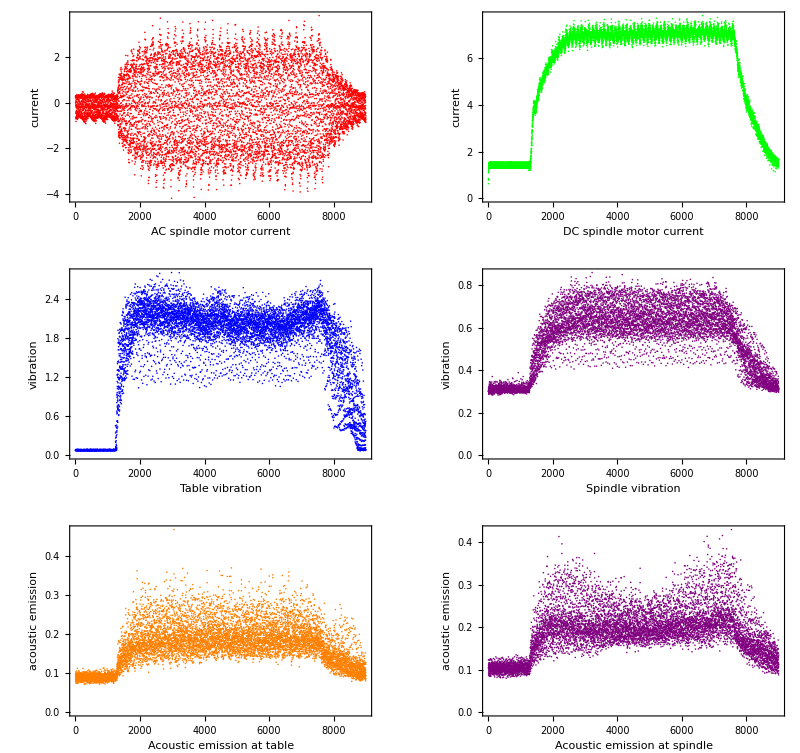

```mathematica
smcACPlot=ListPlot[smcAC,PlotStyle->Red,Frame->True,FrameLabel->{"AC spindle motor current","current"}];
smcDCPlot=ListPlot[smcDC,PlotStyle->Green,Frame->True,FrameLabel->{"DC spindle motor current","current"}];
vibTablePlot=ListPlot[vibTable,PlotStyle->Blue,Frame->True,FrameLabel->{"Table vibration","vibration"}];
vibSpindlePlot=ListPlot[vibSpindle,PlotStyle->Purple,Frame->True,FrameLabel->{"Spindle vibration","vibration"}];
AETablePlot=ListPlot[AETable,PlotStyle->Orange,Frame->True,FrameLabel->{"Acoustic emission at table","acoustic emission"}];
AESpindlePlot=ListPlot[AESpindle,PlotStyle->Purple,Frame->True,FrameLabel->{"Acoustic emission at spindle","acoustic emission"}];
GraphicsGrid[{{smcACPlot,smcDCPlot},{vibTablePlot,vibSpindlePlot},{AETablePlot,AESpindlePlot}}]
```